```mathematica
ComplexQ=NumericQ@#&&#∈Complexes&;
RealQ=NumericQ@#&&#∈Reals&;

Unprotect[Axis];
Axis[x_,y_]:=Module[{l,r,b,t},
{l,r}=If[ListQ[x],x,{-x,x}];
{b,t}=If[ListQ[y],y,{-y,y}];
{Gray,Arrow[{{l,0},{r+0.02,0}}],Arrow[{{0,b},{0,t+0.02}}]}
];

Unprotect[Text];
Text[t_String,p:_?ComplexQ:0,s:_?RealQ:16]:=Text[Style[t,FontSize->s,FontFamily->"Times"],{Re@p,Im@p}];

Unprotect[Line];
Line[z1_?ComplexQ,z2_?ComplexQ]:=Line[{{Re@z1,Im@z1},{Re@z2,Im@z2}}];
Line[o_?ComplexQ,t_?RealQ,d_?RealQ]:=Line[o,o+d E^(t I)];

Arc[z_?ComplexQ,r_?RealQ,dir:_?(RealQ@#&&#!=0&):-1]:=Arc[{{Re@z,Im@z},r,dir}];

Poles=Poles;
Options[Contour]={Poles->{}};
Contour[l_List,OptionsPattern[]]:=Catch@Module[{result={},inters={},FixPath,getIntersection,getAngle},
FixPath[g_]:=If[Head@g===Line,g,Circle[g[[1,1]],g[[1,2]]]];
getIntersection[g1_,g2_]:=Module[{sol},
Off[NSolve::ratnz];
sol=NSolve[{#1,#2}∈FixPath@g1&&{#1,#2}∈FixPath@g2,{#1,#2}];
On[NSolve::ratnz];
If[Length@sol===0,Return[]];
If[Length@sol>1,Print["More than 1 intersection. The value of the first one will be returned."]];
({#1,#2}/.sol)[[1]]
];
getAngle[z_]:=If[Im@z>=0,Arg[z],Arg[z]+2π];
If[Length@l===0,Throw[Null]];
If[Length@l===1,
Print["TODO"];
Throw[Null];
];
If[!MatchQ[l=Flatten@l,{__?(MemberQ[{Line,Arc},Head@#]&)}],
Print["Exist invalid path. All paths must be one of Line and Arc."];
Throw[Null];
];
Do[
AppendTo[inters,getIntersection[l[[i]],l[[i+1]]]];
If[Last@inters===Null,
Print["Exist disjoint paths. Adjacent paths must intersect."];
Throw[Null];
],
{i,Length@l-1}
];
PrependTo[inters,getIntersection[First@l,Last@l]];
AppendTo[inters,First@inters];
Block[{p1,p2,o,r,dir,t1,t2},
Do[
p1=If[inters[[i]]=!=Null,inters[[i]],l[[i,1,1]]];
p2=If[inters[[i+1]]=!=Null,inters[[i+1]],l[[i,1,2]]];
If[Head@l[[i]]===Line,
AppendTo[result,Line[{p1,p2}]],
{o,r,dir}=l[[i,1]];
{t1,t2}=getAngle/@Complex@@@{p1-o,p2-o};
If[t1===t2,Print["Path has the same start and end point, it will be ignored."]];
If[t1<t2&&dir>0,t1+=2π];
If[t1>t2&&dir<0,t2+=2π];
AppendTo[result,Line[Table[{o[[1]]+r Cos[t],o[[2]]+r Sin[t]},{t,t1,t2,Sign[-dir]0.01}]]];
],
{i,Length@l}
]
];
{
Thick,Arrowheads[{{Automatic,0.5}}],Arrow/@result,
{Disk[{Re@#,Im@#},0.01],Text[ToString@#,#-0.045I,14]}&/@OptionValue[Poles]
}
];
```

```mathematica
(*****************************************************************************************************************)
```

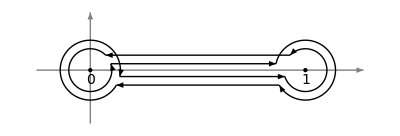

```mathematica
Graphics[{
Axis[{-0.25,1.25},0.25],
Contour[{
Line[-0.03I,0,1],
Arc[1,0.1],
Line[1+0.07I,π,1],
Arc[0,0.1],
Line[0.03I,0,1],
Arc[1,0.14,+1],
Line[1-0.07I,π,1],
Arc[0,0.14,+1]
},Poles->{0,1}]
}]
```